# Analyzing Peg Solitaire Game Boards using Multiway Graphs

Peg Solitaire, also known as Cracker Barrel, is a game played on a board consisting of a number of holes of which all but one are filled with a peg. These boards are usually symmetrical, in shapes such as equilateral  triangles or thick crosses. The goal of the game is to remove all but one peg by jumping pegs over each other, from one side of a peg hole to a free space, removing the peg which was jumped over. This project hopes to model different game boards of peg solitaire, with different board shapes and starting arrangements of pegs, and use their multiway graphs to find a board shape in which there is only one possible solution, or where you must play a perfect game to be able to win, and to see if there are board shapes wherein the game is impossible to solve. 
[expand] [look at abstract of: https://community.wolfram.com/groups/-/m/t/2963967?p_p_auth=61FL9Z8g]

## Peg Solitaire

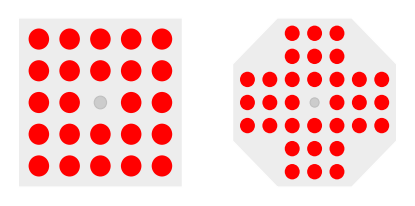

how to play peg solitaire rules ect. 

Sample Game:

```mathematica
ListAnimate[Table[{{"[◼]", "PegSolitaireGraphics"}}[samplecoords][state], {state, {{0,1,1,1,1,1,1,1},{1,1,1,0,1,0,1,1},{1,0,0,1,1,0,1,1},{0,0,0,0,1,1,1,1},{0,0,1,0,0,1,1,0},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1}}}]]
```

[more about modeling the game and peg solitaire graphics]

```mathematica
graphgen[start_,moves_ ]:={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

## Creating Multiway Graphs

[explanation of multiway graphs with some graphics or something]

Maps each coordinate pair to a “name” based on their index

```mathematica
coordnames[coords_] := MapIndexed[#1->#2[[1]]&,coords]
```

multiway graph 1, this takes in a list of coordinate pairs, a starting board state, and a list of possible moves that can be made on the board. Outputs a full multiway graph of the board

```mathematica
multiwaygraph[coords_, start_, moves_] := Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]
```

### Removing “Duplicate” Board States Using Image Transformations

3 functions which work together to generate a list of “unique” board states given a list of states based on their image data. This only works on square and cross shaped boards and is very slow.

```mathematica
compareImg[img1_, img2_]:=If[Length[DominantColors[ImageDifference[ImageRotate[img1, 90 Degree], img2]]] ==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 180 Degree], img2]]]==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 270 Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageReflect[img1], img2]]]==1||
Length[DominantColors[ImageDifference[ImageReflect[img1, Left], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],90Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],180Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],270Degree], img2]]]==1,
True, False]
```

```mathematica
uniqueImg[img_, uniques_] := Which[Length[uniques] ==1, Not[compareImg[img, uniques[[1]]]],
Position[compareImg@@@Partition[Riffle[uniques,img, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
getUnique[stateimglist_] := 
Block[{states = stateimglist, uniques = {stateimglist[[1]]}},
If[uniqueImg[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

This function has the same inputs as multiway graph 1, but only shows “unique” board states in the multiway graph by testing using their images
It’s quite slow, and only works with square and cross boards

```mathematica
multiwayImageCheck[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareImg[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#1], {{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#2]] ==True&]]
]
```

### Removing “Duplicate” Board States Using Matrix Transformations

functions which work together to compare lists of board states to see if they are unique using matrix transformations. Much faster than the image method

```mathematica
compareSqrList[list1_, list2_] := Module[{length = Sqrt[Length[list1]]},
lists1 = Partition[list1, length];
lists2 = Partition[list2, length];
If[Transpose @(Reverse/@lists1)==lists2 ||
Reverse/@(Transpose @lists1)==lists2 ||
Transpose @(Reverse/@(Transpose @(Reverse/@lists1)))==lists2 ||
Transpose @(Reverse/@(Transpose @lists1)) == lists2||
Reverse/@(Transpose @(Reverse/@lists1)) == lists2||
Transpose @lists1 ==lists2 ||
Reverse/@lists1 ==lists2
,True,False]
]
```

```mathematica
(* checks if a board is already represented in a list *)
uniqueboard[board_, uniques_] := Which[Length[uniques] ==1, Not[compareSqrList[board, uniques[[1]]]],
Position[compareSqrList@@@Partition[Riffle[uniques,{board}, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
(* create a list of unique elements *)
getUniqueBoards[statelist_] := 
Block[{states = statelist, uniques = {statelist[[1]]}},
If[uniqueboard[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

Similar to multiway graph 2, this function only shows “unique” board states, but runs much fast due to the fact it utilizes matrix transformations. It only works on square boards and some cross boards.

```mathematica
multiwayMatrixCheck[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

### Generating All Possible Moves

triangle data:

```mathematica
triangle = {makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2}}],
makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}}], makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9},{10,10},{8,10},{6,10},{4,10},{2,10},{0,10},{-2,10},{-4,10},{-6,10},{-8,10},{-10,10}}]}
```

{makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4},{5,5},{3,5},{1,5},{-1,5},{-3,5},{-5,5}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4},{5,5},{3,5},{1,5},{-1,5},{-3,5},{-5,5},{6,6},{4,6},{2,6},{0,6},{-2,6},{-4,6},{-6,6}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4},{5,5},{3,5},{1,5},{-1,5},{-3,5},{-5,5},{6,6},{4,6},{2,6},{0,6},{-2,6},{-4,6},{-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4},{5,5},{3,5},{1,5},{-1,5},{-3,5},{-5,5},{6,6},{4,6},{2,6},{0,6},{-2,6},{-4,6},{-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3},{-3,3},{4,4},{2,4},{0,4},{-2,4},{-4,4},{5,5},{3,5},{1,5},{-1,5},{-3,5},{-5,5},{6,6},{4,6},{2,6},{0,6},{-2,6},{-4,6},{-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9},{10,10},{8,10},{6,10},{4,10},{2,10},{0,10},{-2,10},{-4,10},{-6,10},{-8,10},{-10,10}}]}

square data:

```mathematica
square = {makeimg[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2}, {1,3}, {2,3},{3,3}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}}],makeimg[{{2,1},{3,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{2,4},{3,4}}] ,makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{1,5},{2,5},{3,5},{4,5},{5,5}}], makeimg[{{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{2,5},{3,5},{4,5}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6}}],makeimg[{{3,1},{4,1},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{3,5},{4,5},{3,6},{4,6}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7}}],makeimg[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8}}],makeimg[{{3,1},{4,1},{5,1},{6,1},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{3,7},{4,7},{5,7},{6,7},{3,8},{4,8},{5,8},{6,8}}]}
```

{makeimg[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}}],makeimg[{{2,1},{3,1},{1,2},{2,2},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{2,4},{3,4}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{1,5},{2,5},{3,5},{4,5},{5,5}}],makeimg[{{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{2,5},{3,5},{4,5}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6}}],makeimg[{{3,1},{4,1},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{3,5},{4,5},{3,6},{4,6}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7}}],makeimg[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8}}],makeimg[{{3,1},{4,1},{5,1},{6,1},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{3,7},{4,7},{5,7},{6,7},{3,8},{4,8},{5,8},{6,8}}]}

```mathematica
(* makes an image that shows points given by a list of coordinates *)
makeimg[points_ ] := 
Graphics[{PointSize[Large],Point[Table[p,{p,points}]]}]
```

```mathematica
checkshape = Classify[<|"square" -> square, "triangle" ->triangle|>]
```

ClassifierFunction[…]

```mathematica
(* calculates the points next to a specified peg given the coordinates of a square*)
getNear[coords_ , peg_, shape_String:"square" ]/;shape=="square"&&Head[coords[[1]]]==List:= Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] == 1 && (coord[[1]] == peg[[1]] || coord[[2]] == peg[[2]]), coord],{coord, coords}], ListQ]]
```

```mathematica
(* getNear but for a triangle *)
getNear[coords_ , peg_, shape_String:"square"]/;shape=="triangle" &&Head[coords[[1]]]==List:= Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 || And[peg[[2]]==coord[[2]],EuclideanDistance[peg, coord] == 2], coord],{coord, coords}], ListQ]]
```

```mathematica
pegMoves[initalpeg_, coordlist_ /;Head[coordlist[[1]]]==List]:=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg, checkshape[makeimg[coords]]];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ]
]
```

```mathematica
(* maps through all pegs in a peg list and find all possible moves *)
allMoves[coordlist_/;Head[coordlist[[1]]]==List] := Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, coords] /. coordnames[coords] &/@ coords];
DeleteDuplicates[Flatten[moves,1], Length[#1∪#2] ==3 &]
]
```

### Manipulating Graphs

```mathematica
cropGraph[fullgraph_, maxpins_,minpins_ ,coords_, xsquish_:1,ysquish_:2, size_:1.2] :=Graph[Graph[Cases[Table[If[ Position[Select[Table[If[Length[Position[vertex,1]]<=maxpins&&Length[Position[vertex,1]]>=minpins,vertex], {vertex, VertexList[fullgraph]}],ListQ],edge[[1]]]!={}, edge],{edge, EdgeList[fullgraph]}], Except[Null]]],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->size,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3, VertexCoordinates->Rule @@@Partition[Riffle[VertexList[fullgraph],Table[{(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[1]]/xsquish,(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[2]]/ysquish },{i, Range[Length[(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])]]}]],2]]
```

```mathematica
Manipulate[cropGraph[-Graphics-,max,min,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{max,9,min,1,Appearance->"Labeled"},{min,2,max,1,Appearance->"Labeled"}, ContinuousAction->False]
```

```mathematica
manipulateGraph[fullgraph_, coords_, xsquish_:1,ysquish_:2, size_:1.2] :=Graph[fullgraph,VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->size,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3, VertexCoordinates->Rule @@@Partition[Riffle[VertexList[fullgraph],Table[{(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[1]]/xsquish,(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[2]]/ysquish },{i, Range[Length[(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])]]}]],2]]
```

## Analyzing 3 by 3 Boards

```mathematica
(* all "starting board" states which lead to a multiway graph longer than 2 *)
threecoords = {{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}};
threemoves = allMoves[threecoords];
allthrees = SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>2, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount];
solutionthrees = SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>2 && Length[Position[VertexList[multiwayMatrixCheck[threecoords, state, threemoves]][[-1]],1]]==1, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount];
```

same number of boards when there’s 1 hole and when there is 9, 2 - 7, 3 - 6, 4 - 5

```mathematica
Manipulate[GraphicsRow[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Permutations[Join[Range[9-holes]/. _Integer->1, Range[holes]/. _Integer->0 ]]]}]],{holes, 1,8,1}, ]
```

### All Possible Multiway Graphs

```mathematica
Manipulate[Select[allthrees, VertexCount[#]==moves&],{moves, 3,10,1}]
```

```mathematica
(* all "starting board" states which lead to a solution *)
SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>1 && Length[Position[VertexList[multiwayMatrixCheck[threecoords, state, threemoves]][[-1]],1]]==1, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 3 By 3 Boards with Holes

```mathematica
pegMoves[initalpeg_, coordlist_/;Head[coordlist[[1]]]==Rule] :=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ] 
]
```

```mathematica
allMoves[coordlist_ /;Head[coordlist[[1]]]==Rule]:= Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, Keys[coords]] /. coords &/@ Keys[coords]];
DeleteDuplicates[Flatten[moves,1], Length[#1∪#2] ==3 &]
]
```

```mathematica
holeBoardPerms[holes_Integer, boardsize_Integer/;IntegerQ[Sqrt[boardsize]],blanks_:1] := 
getUniqueBoards[Permutations[Join[Range[boardsize-holes-blanks]/._Integer->1, Range[holes]/._Integer->3, Range[blanks]/._Integer->0]]]
```

```mathematica
holeBoardCoords[coords_, state_] :=Select[coordnames[threecoords],state[[#[[2]]]]!=3&]
```

```mathematica
(* not sure i wanna keep *)
Manipulate[Table[{{"[◼]", "PegSolitaireGraphics"}}[holeBoardCoords[threecoords, perm]][perm],{perm, getUniqueBoards[holeBoardPerms[holes,9]]}],{holes, 1,7,1},ContinuousAction->False, SaveDefinitions->True]
```

```mathematica
(* multiway graph creater for boards with holes (takes in coordlist WITH names) *)
multiwaygraph4[coordlist_, starting_, allmoves_] := Module[{coords = coordlist, start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], coords];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

```mathematica
GraphicsRow[Select[Table[If[VertexCount[multiwaygraph4[holeBoardCoords[threecoords, perm], perm, allMoves[holeBoardCoords[threecoords, perm]]]]>=3,multiwaygraph4[holeBoardCoords[threecoords, perm], perm, allMoves[holeBoardCoords[threecoords, perm]]]],{perm,holeBoardPerms[1,9]}], GraphQ]]
```

-Graphics-

## Expanding 3 by 3’s to Larger Boards

```mathematica
threecoords = ;
fourcoords = ;
fourmoves = allMoves[fourcoords];
fivecoords = ;
fivemoves = allMoves[fivecoords];
```

```mathematica
getFiveCoords[graph_] :=Flatten[Prepend[Append[Table[Flatten[Prepend[Append[Partition[VertexList[graph][[1]],3][[i]],0],0]],{i, Range[3]}],{0,0,0,0,0}],{0,0,0,0,0}]]
```

Three by Threes expanded to 5 x 5 boards

```mathematica
getFourCoords[graph_, tb_, rl_]/;tb==1 && rl==1 :=Flatten[Append[Table[Flatten[Append[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==1 && rl==0 :=Flatten[Append[Table[Flatten[Prepend[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==0 && rl==1 :=Flatten[Prepend[Table[Flatten[Prepend[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==0 && rl==0 :=Flatten[Prepend[Table[Flatten[Append[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
```

```mathematica
graph = -Graphics-;
```

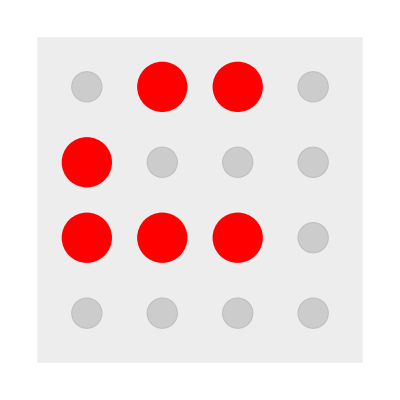
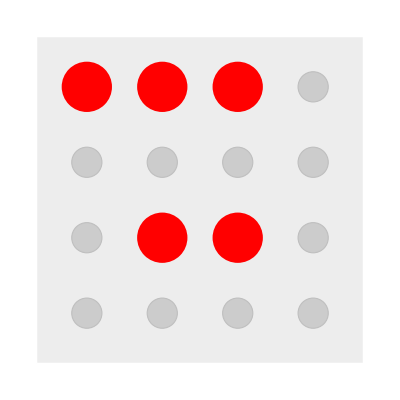
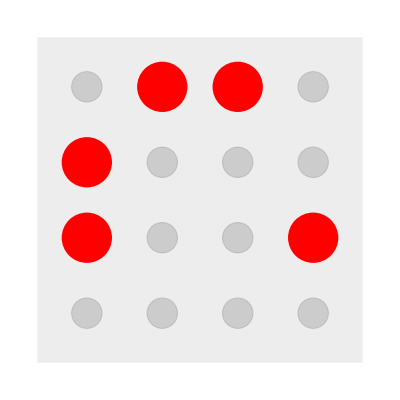
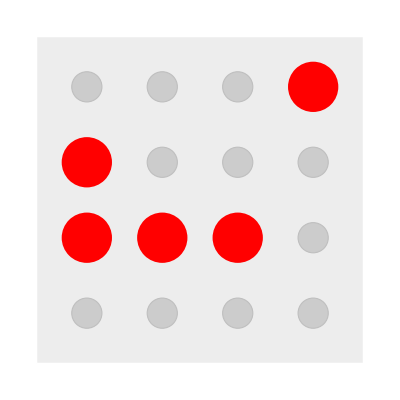
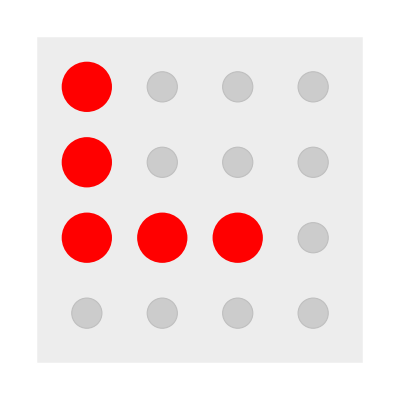
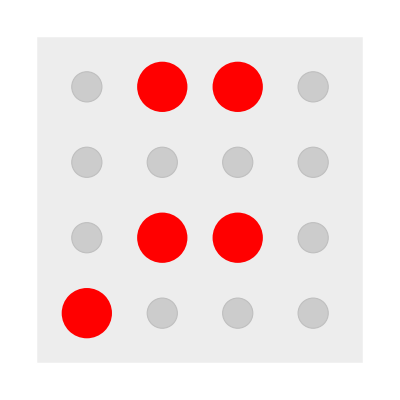
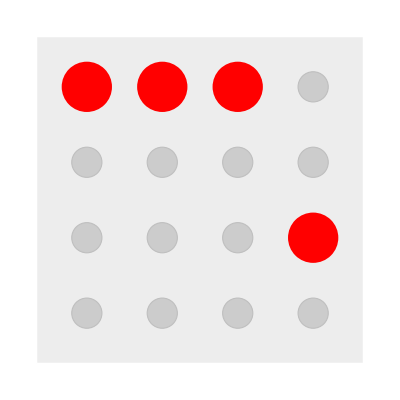
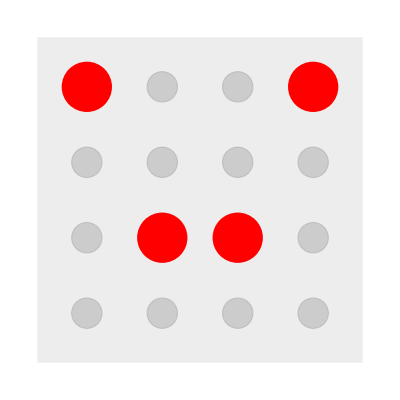
{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[multiwaygraph3[fourcoords, state, allMoves[fourcoords]], {state, Table[getFourCoords[graph, perm[[1]],perm[[2]]],{perm, {{0,0},{0,1},{1,0},{1,1}}}]}]
```

```mathematica
GraphicsRow[Table[multiwayMatrixCheck[fourcoords, state, allMoves[fourcoords]], {state, Table[getFourCoords[graph, perm[[1]],perm[[2]]],{perm, {{0,0},{0,1},{1,0},{1,1}}}]}]]
```

-Graphics-

```mathematica
fivegraph = multiwaygraph[fivecoords, getFiveCoords[-Graphics-], allMoves[fivecoords]];
```

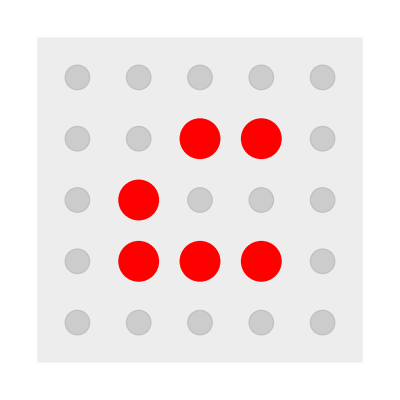
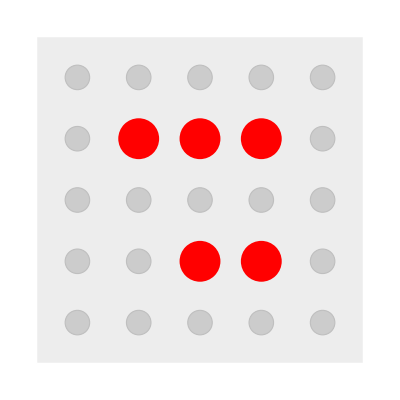
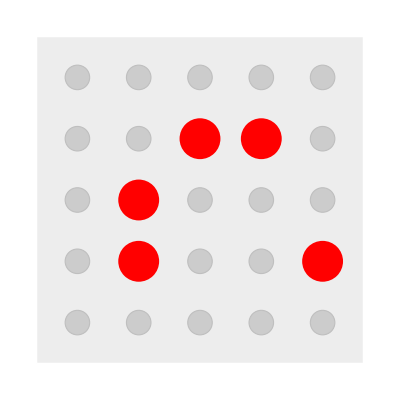
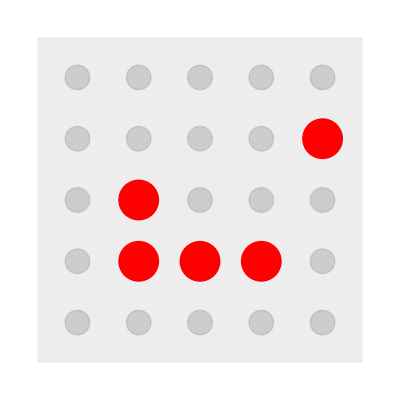
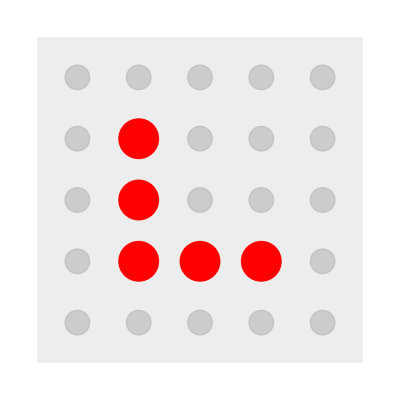
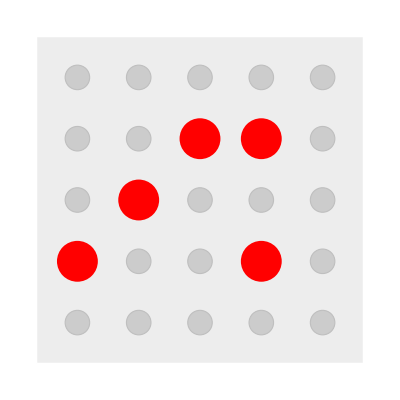
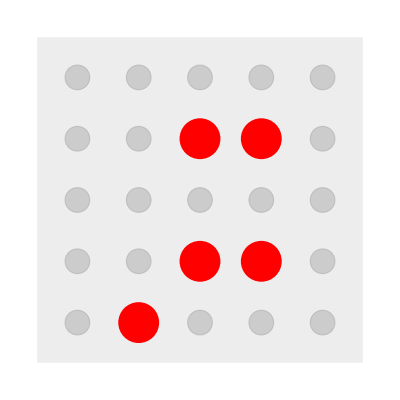
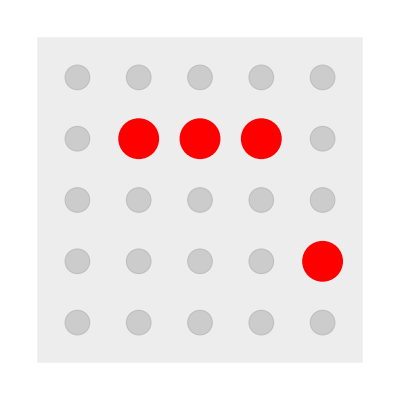

```mathematica
manipulateGraph[fivegraph, fivecoords,1.5,6,1.5]
```

### Comparing 4 x 4 and 5 x 5 Boards

```mathematica
fourToFive[list_, tb_, rl_]/;tb==1 && rl==1:=Flatten[Append[Table[Append[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==1 && rl==0:=Flatten[Append[Table[Prepend[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==0 && rl==1:=Flatten[Prepend[Table[Append[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==0 && rl==0:=Flatten[Prepend[Table[Prepend[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
```

```mathematica
fourFiveGraphHighlight[fivegraph_, fourgraph_, tb_, rl_, xsquish_:1, ysquish_:2, size_:1.5] :=manipulateGraph[HighlightGraph[fivegraph,DeleteCases[Table[If[Position[Intersection[VertexList[fivegraph], Table[fourToFive[VertexList[fourgraph][[i]],tb,rl],{i, Range[Length[VertexList[fourgraph]]]}]],EdgeList[fivegraph][[i]][[2]]]!={},EdgeList[fivegraph][[i]]],{i,Length[EdgeList[fivegraph]]}],Null]], fivecoords,xsquish,ysquish,size]
```

```mathematica
Manipulate[fourFiveGraphHighlight[-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2],{{graph,{multiwayMatrixCheck[fourcoords, Range[16]/. _Integer->0, fourmoves],{1,0}} ," "},{{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,{1,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{1,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]}}]
```